# Loading Initial Results

The results were exported from the simulation application as multiple 2D arrays of entries, each entry is 5 parameters in double precision format:
	• Lobe θ
	• Lobe roughness α
	• Lobe Scale σ
	• Lobe non-uniform Scale σ_n (also called “flattening factor”)
	• Lobe masking importance m

Each 2D array corresponds to a different albedo, there are currently 4 surface albedos that were simulated: 1, 0.75, 0.5 and 0.25
We’re currently focusing on 2nd order scattering since models for 1st order scattering are quite well documented already.

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]](* So Mathematica knows the directory for our files *)
str=OpenRead["results_order2_slice0.bin",{BinaryFormat->True}]
rawFile0= BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
Close[str];
```

D:\Workspaces\GodComplex\Tools\TestMSBSDF\Results\Diffuse\0) Initial Fitting\Export

InputStream[…]

```mathematica
str=OpenRead["results_order2_slice1.bin",{BinaryFormat->True}]
rawFile1= BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
Close[str];
```

InputStream[…]

```mathematica
str=OpenRead["results_order2_slice2.bin",{BinaryFormat->True}]
rawFile2= BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
Close[str];
```

InputStream[…]

```mathematica
str=OpenRead["results_order2_slice3.bin",{BinaryFormat->True}]
rawFile3= BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
Close[str];
```

InputStream[…]

```mathematica
(* Organize raw list into a proper 2D array depending on suface's theta/roughness *)
resX=20;
resY=10;
table0=Table[rawFile0[[1+(20*j)+i]],{j,0,resY-1},{i,0,resX-1}];
table1=Table[rawFile1[[1+(20*j)+i]],{j,0,resY-1},{i,0,resX-1}];
table2=Table[rawFile2[[1+(20*j)+i]],{j,0,resY-1},{i,0,resX-1}];
table3=Table[rawFile3[[1+(20*j)+i]],{j,0,resY-1},{i,0,resX-1}];
MatrixForm[table0];
```

```mathematica
table0[[10,20]]
```

{0.,1.,1.×10^-6,1.,0.}

# Parametrization of Θ

```mathematica
paramsTheta0 = Table[table0[[j]][[i]][[1]],{j,1,resY},{i,1,resX}];
paramsTheta1 = Table[table1[[j]][[i]][[1]],{j,1,resY},{i,1,resX}];
paramsTheta2 = Table[table2[[j]][[i]][[1]],{j,1,resY},{i,1,resX}];
paramsTheta3 = Table[table3[[j]][[i]][[1]],{j,1,resY},{i,1,resX}];
MatrixForm[paramsTheta0]
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
Show[ListPlot3D[paramsTheta0,{ColorFunction->Red,ColorFunctionScaling->False, PlotRange->{0,π/2}}],
ListPlot3D[paramsTheta1,{ColorFunction->RGBColor[0,1,0],PlotRange->{0,π/2}}],
ListPlot3D[paramsTheta2,{ColorFunction->RGBColor[0,0,1],PlotRange->{0,π/2}}],
ListPlot3D[paramsTheta3,{ColorFunction->RGBColor[1,1,0],PlotRange->{0,π/2}}] ]
```

-Graphics3D-

No surprise there : the diffuse lobe is almost static and has no prefered direction so θ = 0 ⟹ One less parameter to worry about!
NOTE: Now it’s completely flat because I really constrained the θ parameter to 0 in subsequent simulations.

# Parametrization of the Lobe’s Flattening Factor

```mathematica
paramsFlat0 = Table[table0[[j]][[i]][[4]],{j,1,resY},{i,1,resX}]
paramsFlat1 = Table[table1[[j]][[i]][[4]],{j,1,resY},{i,1,resX}];
paramsFlat2 = Table[table2[[j]][[i]][[4]],{j,1,resY},{i,1,resX}];
paramsFlat3 = Table[table3[[j]][[i]][[4]],{j,1,resY},{i,1,resX}];
```

{{0.724906,0.688076,0.701907,0.703759,0.710605,0.709456,0.697577,0.692891,0.676963,0.708963,0.700425,0.724138,0.706265,0.719578,0.715832,0.763943,0.777823,0.817766,0.851497,0.969522},{0.646509,0.666957,0.65783,0.654693,0.649588,0.648088,0.638525,0.663808,0.659816,0.634433,0.639504,0.63819,0.64631,0.639801,0.666222,0.687335,0.709513,0.75615,0.801344,0.905199},{0.586855,0.589525,0.598961,0.5981,0.597807,0.575982,0.589513,0.601969,0.587275,0.597156,0.582062,0.600009,0.601582,0.601568,0.568418,0.606355,0.63416,0.664701,0.705999,0.840973},{0.537748,0.539268,0.535908,0.538814,0.530719,0.526818,0.514291,0.532246,0.546436,0.53938,0.533537,0.539316,0.536631,0.520191,0.532991,0.550933,0.570078,0.589654,0.624473,0.737687},{0.491792,0.484248,0.445369,0.493784,0.491377,0.498086,0.28799,0.489388,0.484403,0.490464,0.494296,0.486338,0.494888,0.501757,0.492273,0.497683,0.504432,0.489873,0.549845,0.629639},{0.445614,0.433832,0.446477,0.441891,0.449231,0.437717,0.43656,0.447149,0.431754,0.428211,0.447703,0.443431,0.448935,0.43816,0.448138,0.453895,0.45124,0.477058,0.479793,0.556272},{0.404176,0.400367,0.397957,0.401087,0.399882,0.398403,0.399322,0.398071,0.386743,0.400036,0.397849,0.395728,0.399823,0.402813,0.404504,0.403278,0.403049,0.406877,0.412467,0.486426},{0.34214,0.329573,0.339629,0.339938,0.339766,0.339775,0.336181,0.33798,0.337977,0.339337,0.320845,0.339279,0.341616,0.333789,0.343077,0.33966,0.33916,0.343387,0.346427,1.0012},{1.00081,1.00081,1.00081,1.00081,1.00081,1.00081,1.00081,1.00081,1.00081,1.00081,1.0008,1.00081,1.0008,1.00081,1.00081,1.00081,1.00081,1.00081,1.00081,1.00018},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
ListPlot3D[paramsFlat0,{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}}]
ListPlot3D[paramsFlat1,{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}}]
ListPlot3D[paramsFlat2,{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}}];
ListPlot3D[paramsFlat3,{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}}];
```

-Graphics3D-

-Graphics3D-

We see that for albedo 1 and 0.75, the shape is pretty similar (assuming precision errors for low roughness) and that for lower albedos the change was neglected and is always 1.
We thus concentrate on albedo 1 to fit what seems to be a pretty straightforward shape, except when roughness becomes low in which case the fitter resorted to the default value and modified the other parameters instead.
So basically our range of confidence in ρ is from index 1 to about 6.

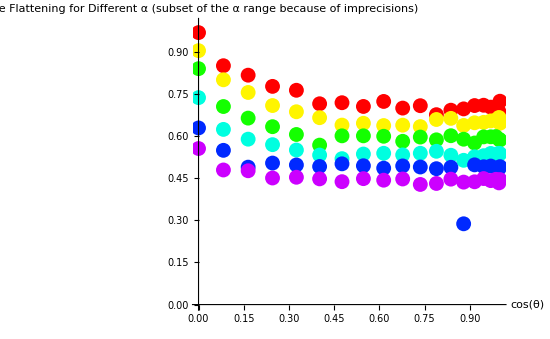

```mathematica
test=Table[{(i-1)/(resX-1),  paramsFlat0[[1]][[i]]},{i,1,resX}];
ListPlot[test];
valuesSn=Table[Table[{Cos[(i-1)/(resX-1)*π/2],paramsFlat0[[j]][[i]]},{i,1,resX}],{j,1,6}];
Show[Table[ListPlot[valuesSn[[i]],PlotRange->{0,1} , PlotStyle->Hue[0.16*(i-1)],AxesLabel->{"cos(θ)","Lobe Flattening for Different α\n(subset of the α range because of imprecisions)"}],{i,1,6}]]
```

(a→0.699336 | b→0.264057 | c→5.28373
a→0.646501 | b→0.2611 | c→6.07679
a→0.591226 | b→0.247842 | c→8.32299
a→0.533366 | b→0.201661 | c→8.34108
a→0.473773 | b→0.150725 | c→7.78062
a→0.441773 | b→0.111167 | c→9.40142)

(0.699336+0.264057 ⅇ^(-5.28373 u)
0.646501+0.2611 ⅇ^(-6.07679 u)
0.591226+0.247842 ⅇ^(-8.32299 u)
0.533366+0.201661 ⅇ^(-8.34108 u)
0.473773+0.150725 ⅇ^(-7.78062 u)
0.441773+0.111167 ⅇ^(-9.40142 u))

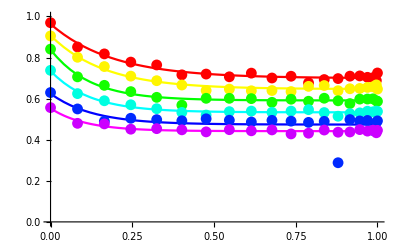

```mathematica
modelSn=a+b*Exp[-c * u];
fittingSn = Table[FindFit[ valuesSn[[j]],modelSn,{a,b,c},u ],{j,1,6}];
MatrixForm[fittingSn]
MatrixForm[modelSn/.fittingSn]
Show[Table[Plot[modelSn/.fittingSn[[j]],{u,0,1},PlotRange->{0,1},PlotStyle->Hue[(j-1)/6]],{j,1,6}],
Table[ListPlot[valuesSn[[i]],PlotRange->{0,1} , PlotStyle->Hue[0.16*(i-1)]],{i,1,6}]]
```

#### Matching Parameters

Now that we have a bunch of nice expressions for representing f(cos(θ)), we need to find tendencies in the fitted parameters a, b and c.

0.697462-0.479278 x

0.287646-0.293594 x

5.69744+6.61321 x

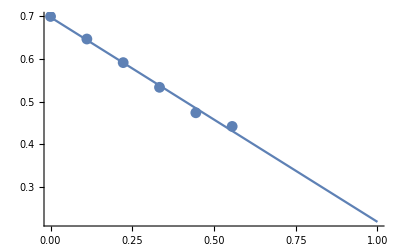

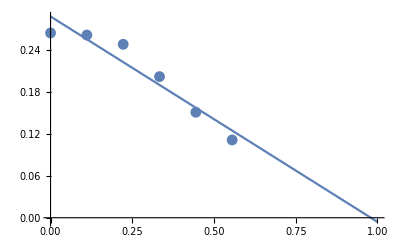

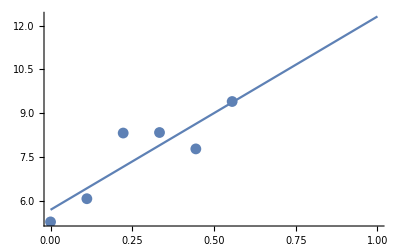

```mathematica
fa = Table[{(j-1)/9,a/.fittingSn[[j]]}, {j,1,6}];
fb = Table[{(j-1)/9,b/.fittingSn[[j]]}, {j,1,6}];
fc= Table[{(j-1)/9,c/.fittingSn[[j]]}, {j,1,6}];
mfa = LinearModelFit[fa,x,x];
mfb = LinearModelFit[fb,x,x];
mfc = LinearModelFit[fc,x,x];
Normal[mfa]
Normal[mfb]
Normal[mfc]
Show[ListPlot[fa,PlotRange->{0,1}],Plot[mfa[x],{x,0,1}],PlotRange->All]
Show[ListPlot[fb,PlotRange->{0,1}],Plot[mfb[x],{x,0,1}],PlotRange->All]
Show[ListPlot[fc,PlotRange->{0,10}],Plot[mfc[x],{x,0,1}],PlotRange->All]
```

#### Final Expression

We can now obtain the final expression for the function matching the lobe flattening factor:

a(α) = 0.697462 - 0.479278 α
b(α) = 0.287646 - 0.293594 α
c(α) = 5.69744 + 6.61321 α
μ = cos(θ)
f( μ, α ) = a(α) + b(α) e^(-c(α)  μ)

```mathematica
a[α_] = 0.697462 - 0.479278 α;
b[α_] = 0.287646 - 0.293594 α;
c[α_] = 5.69744 + 6.61321 α;
f[ μ_, α_] = a[α] + b[α] Exp[-c[α]  μ];

Plot3D[f[μ,α],{μ,0,1},{α,0,1},PlotRange->{0,1},AxesLabel->{"cos(θ)","α","Lobe Flattening"}]
```

-Graphics3D-

#### Checking our Matching

```mathematica
Show[
ListPlot3D[ paramsFlat0,PlotRange->{0,1},AxesLabel->{"θ","α"},PlotStyle->Blue],
Plot3D[f[Cos[(i-1)/(resX-1)π/2],(j-1)/(resY-1)],{i,1,resX},{j,1,resY},PlotStyle->Red]
]
```

-Graphics3D-

Pretty good! 
Now we can remove that parameter from the simulation and use our fitting instead. That should help us stabilize the other parameters...